# Finite difference quasireversible chronopotentiometry

## Fully explicit method

This notebook shows how a chronopotentiogram for the simple quasireversible reaction A + e ⇌ B can be simulated using explicit finite difference methods.

Version 2.0
copyright © 2002-Year Michael Honeychurch

## Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"],Clear["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
Off[FindRoot::"cvnwt"];
```

```mathematica
SetOptions[ListPlot,
Axes->False,
FormatType->TraditionalForm,
FrameLabel->None,
Frame->True,
FrameStyle->{ColorData["Legacy","NavyBlue"],AbsoluteThickness[.5]},FrameTicks->Automatic,
GridLines->None,
ImageSize->288,
Joined->True,
PlotLabel->None];
```

```mathematica
xTicks1[min_,max_]:=Join[Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],Ceiling[max]/4//N}],Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-Ceiling[max]/4//N}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],Ceiling[max]/20//N}]];

yTicks2[min_,max_]:=Join[Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],Ceiling[max]/2//N}],Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-Ceiling[max]/2//N}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],Ceiling[max]/10//N}]];

xTicks3[min_,max_]:=Join[Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],Ceiling[max]/4}],Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-Ceiling[max]/4}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],Ceiling[max]/20}]];

yTicks4[min_,max_]:=Join[Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],Ceiling[max]/2}],Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-Ceiling[max]/2}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],Ceiling[max]/10}]];
```

```mathematica
optionA={
PlotStyle-> {Red,AbsoluteThickness[0.5]},FrameTicks-> Automatic,
FrameLabel->{
Style["t",FontFamily-> "Times New Roman",FontColor-> Black,FontSlant-> Italic,FontSize-> 12],Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",FontSlant-> Italic,FontColor->Black,FontSize-> 12],None,None}};
```

```mathematica
$Line=0;
```

## Set Up Solution

```mathematica
Clear[explicitChronoPot4];

explicitChronoPot4[m_Integer,n_Integer,d_,i_,ksDim_,α_]:=Module[{solveFor,solveForSecond,stopFor,stopFor2,eValues,conc,c,c1,iDim,potentials1,potentials2},

conc=ConstantArray[{1.,0.,1.,0.},{m}];
iDim=(2*i)/(√(d*(n-1)));
stopFor[list_List]:=NonNegative[Part[list,1,1]];
stopFor2[list_List]:=NonNegative[Part[list,1,3]];

solveFor[list_List]:=Module[{temp},
temp=ListCorrelate[{{d},{(1.-2.*d)},{d}},conc];
 conc=Partition[Flatten[{(iDim+4*temp⟦1,1⟧-temp⟦2,1⟧)/3,-(iDim-4*temp⟦1,2⟧+temp⟦2,2⟧)/3,temp,1.,0.}],2];
Take[conc,1]
];

solveForSecond[list_List]:=Module[{temp},

temp=ListCorrelate[{{d},{(1.-2.*d)},{d}},conc];
 conc=Partition[Flatten[{0.,1.,(iDim+4*temp⟦1,1⟧-temp⟦2,1⟧+4*temp⟦1,3⟧-temp⟦2,3⟧)/3,(-iDim-3.+4*temp⟦1,2⟧-temp⟦2,2⟧+4*temp⟦1,4⟧-temp⟦2,4⟧)/3,temp,1.,0.,1.,0.}],4];
Take[conc,1]
];


c=Rest@NestWhileList[solveFor,conc,stopFor,1,n,-1];
c=Partition[Flatten[c],4];

eValues=Map[FindRoot[(i/ksDim)==#⟦2⟧*Exp[(1-α)*ℰ]-#⟦1⟧*Exp[-α*ℰ],{ℰ,5.}]&,c];
potentials1=ℰ/.eValues;
conc=Map[{#⟦1⟧,#⟦2⟧,1.,0.}&,conc];
conc=conc/.{conc⟦1,1⟧-> 0.,conc⟦1,2⟧-> 1.};

c1=Rest@NestWhileList[solveForSecond,conc,stopFor2,1,4*n,-1];
c1=Partition[Flatten[c1],4];

eValues=Map[FindRoot[(i/ksDim)==#⟦4⟧*Exp[(1-α)*(ℰ+15)]-#⟦3⟧*Exp[-α*(ℰ+15)],{ℰ,5.}]&,c1];
potentials2=(ℰ/.eValues);
Join[potentials1,potentials2]
]
```

## Set Parameter Values

### Set constants

```mathematica
Clear[F,R,T,f,𝒟,α];

F=96485.(*Faradays constant*);

R=8.3144(*gas constant*);

T=298.(*temperature*);

f=F/(R*T);

𝒟=1.*^-5(*diffusion coefficient*);

α=0.5 (*transfer coefficient*);
```

### Simulation variables

```mathematica
Clear[i,ks,n,𝔻,m,ksDim];

i=-0.9;(*dimensionless current*)

ks=1.*^6;(*standard rate constant*)

n=101;

𝔻=0.35;

m=1+Ceiling[6*√(𝔻*(n-1))];

ksDim=ks*Sqrt[1./(𝒟*𝔻*(n-1.))];(*dimensionless rate constant*)
```

## Solve it

```mathematica
potentials=explicitChronoPot4[m,n,𝔻,i,ksDim,α];//Timing
```

{0.256882,Null}

## Plot Potential v. Time

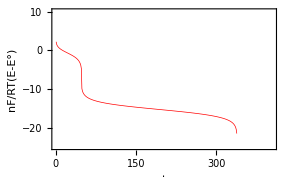

```mathematica
ListPlot[potentials,optionA,PlotRange-> {{1,4*n},{-25,10}}]
```